### Start choosing the example:

```mathematica
t=30;
beta = 0;
A = 0.2;
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
Data["Switching Costs"]={}
```

{}

```mathematica
Data
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,0},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U1}},Switching Costs→{}|>

```mathematica
Keys@MFGEquations
```

{BG,EntranceVertices,InwardVertices,InEdges,ExitVertices,OutwardVertices,OutEdges,AuxiliaryGraph,FG,VL,EL,BEL,FVL,AllTransitions,NoDeadEnds,NoDeadStarts,jargs,js,jvars,jts,jtvars,uargs,us,uvars,SwitchingCosts,OutRules,InRules,EntryArgs,EntryDataAssociation,jays,NonZeroEntryCurrents,ExitCosts,EqCurrentCompCon,EqTransitionCompCon,EqCompCon,EqAllComp,EqPosCon,EqBalanceSplittingCurrents,EqBalanceGatheringCurrents,EqEntryIn,EqExitValues,EqSwitchingConditions,EqValueAuxiliaryEdges,EqAll,EqAllCompRules,EqAllRules,EqAllAll,BoundaryRules,reduced1,reduced2,EqAllAllSimple,RulesEntryIn,RulesExitValues,EqAllAllRules,Nlhs,EqCriticalCase,criticalreduced1,criticalreduced2,Nrhs,EqGeneralCase,TOL}

```mathematica
MFGEquations=DataToEquations[Data/.{I1-> 2, U1-> 0}];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.011961,Null}

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→6,u88→4,u89→2,u90→0,u91→6,u92→-2+6,u93→-2+4,u94→-2+2,u95→0,u96→6|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=Catch @ FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→3.13959,u88→2.09306,u89→1.04653,u90→0,u91→3.13959,u92→2.09306,u93→1.04653,u94→0,u95→0,u96→3.13959|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 3.84593×10^-16

FRX1: The Error on the nonlinear terms is 3.84593×10^-16

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→3.2972,u88→2.19814,u89→1.09907,u90→0,u91→3.2972,u92→2.19814,u93→1.09907,u94→0,u95→0,u96→3.2972|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→3.66483,u88→2.44322,u89→1.22161,u90→0,u91→3.66483,u92→2.44322,u93→1.22161,u94→0,u95→0,u96→3.66483|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.44089×10^-16

FRX1: The Error on the nonlinear terms is 4.44089×10^-16

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→5.50047,u88→3.66698,u89→1.83349,u90→0,u91→5.50047,u92→3.66698,u93→1.83349,u94→0,u95→0,u96→5.50047|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 3.84593×10^-15

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→6,u88→4,u89→2,u90→0,u91→6,u92→4,u93→2,u94→0,u95→0,u96→6|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.69185×10^-16

FRX1: The Error on the nonlinear terms is 7.69185×10^-16

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→7.32794,u88→4.88529,u89→2.44265,u90→0,u91→7.32794,u92→4.88529,u93→2.44265,u94→0,u95→0,u96→7.32794|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 7.69185×10^-16

FRX1: The Error on the nonlinear terms is 7.69185×10^-16

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→10.9282,u88→7.28546,u89→3.64273,u90→0,u91→10.9282,u92→7.28546,u93→3.64273,u94→0,u95→0,u96→10.9282|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→13.0372,u88→8.69147,u89→4.34573,u90→0,u91→13.0372,u92→8.69147,u93→4.34573,u94→0,u95→0,u96→13.0372|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→13.0397,u88→8.69314,u89→4.34657,u90→0,u91→13.0397,u92→8.69314,u93→4.34657,u94→0,u95→0,u96→13.0397|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→49.1196,u88→32.7464,u89→16.3732,u90→0,u91→49.1196,u92→32.7464,u93→16.3732,u94→0,u95→0,u96→49.1196|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→13.1636,u88→8.77571,u89→4.38786,u90→0,u91→13.1636,u92→8.77571,u93→4.38786,u94→0,u95→0,u96→13.1636|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→13.2923,u88→8.86156,u89→4.43078,u90→0,u91→13.2923,u92→8.86156,u93→4.43078,u94→0,u95→0,u96→13.2923|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→13.5573,u88→9.03823,u89→4.51911,u90→0,u91→13.5573,u92→9.03823,u93→4.51911,u94→0,u95→0,u96→13.5573|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

FRX1: The Error on the nonlinear terms is 1.53837×10^-15

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→14.4175,u88→9.61169,u89→4.80584,u90→0,u91→14.4175,u92→9.61169,u93→4.80584,u94→0,u95→0,u96→14.4175|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→16.1117,u88→10.7411,u89→5.37057,u90→0,u91→16.1117,u92→10.7411,u93→5.37057,u94→0,u95→0,u96→16.1117|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→20.9727,u88→13.9818,u89→6.99091,u90→0,u91→20.9727,u92→13.9818,u93→6.99091,u94→0,u95→0,u96→20.9727|>

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 0.

FRX1: The Error on the nonlinear terms is 0.

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→29.6824,u88→19.7883,u89→9.89413,u90→0,u91→29.6824,u92→19.7883,u93→9.89413,u94→0,u95→0,u96→29.6824|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

FRX1: The Error on the nonlinear terms is 6.15348×10^-15

<|j69→2,j70→2,j71→2,j72→2,j73→2,j74→0,j75→0,j76→0,j77→0,j78→0,jt79→0,jt80→2,jt81→2,jt82→0,jt83→2,jt84→0,jt85→2,jt86→0,u87→49.1196,u88→32.7464,u89→16.3732,u90→0,u91→49.1196,u92→32.7464,u93→16.3732,u94→0,u95→0,u96→49.1196|>

### What we this plot for?

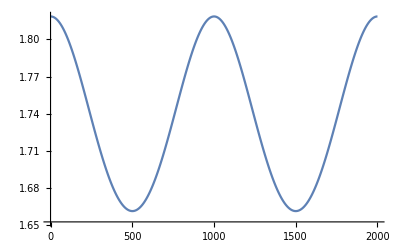

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.